```mathematica
fullFoil = 140;
partialFoil = 100;
womensCut = 70;
mensCut = 48;
keratinExp = 150;
color = 83;
fullFoiliage = 170;
partFoiliage = 140;
shampStyle = 48;
glaze = 20;

Combo1 = womensCut + partialFoil;
Combo2 = womensCut+ color;
Combo3 = womensCut + fullFoil;
Combo4 = womensCut+ keratinExp;
Combo5 = womensCut + fullFoiliage;
Combo6 = womensCut + partFoiliage ;
Combo7 = womensCut + glaze

extraservice1= 0;
extraservice2 = 0;
```

90

```mathematica
TableForm[{{1,Combo5},{2, Combo4},{3,Combo3},{4,Combo6},{5,Combo1},{6,fullFoiliage}, {7,Combo2},{8,keratinExp},{9,fullFoil},{10,partFoiliage},{11,partialFoil},{12,Combo7},{13,color},{14,womensCut},{15,mensCut},{16,shampStyle},{17,glaze}},TableHeadings-> {None,{"Service","Service Total ($)"}}]
```

Service | Service Total ($)
1 | 240
2 | 220
3 | 210
4 | 210
5 | 170
6 | 170
7 | 153
8 | 150
9 | 140
10 | 140
11 | 100
12 | 90
13 | 83
14 | 70
15 | 48
16 | 48
17 | 20

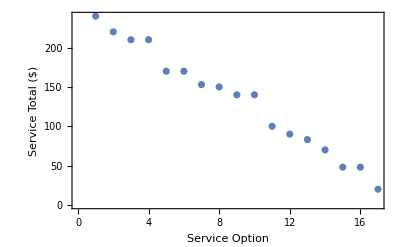

```mathematica
ListPlot[%,Frame->True,FrameLabel->{"Service Option","Service Total ($)"},LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]}, Joined->False]
```

```mathematica
data = Table[{Combo5,Combo4,Combo3,Combo6,Combo1,fullFoiliage,Combo2,keratinExp,fullFoil,partFoiliage,partialFoil,Combo7,color,womensCut,mensCut,shampStyle,glaze}];
data2 = {"Full Foilyage + Cut","Keratin Express + Cut","Full Foil + Cut","Partial Foilyage + Cut","Partial Foil + Cut","Full Foilyage","Cut + Color","Keratin Express","Full Foil","Partial Foilyage","Partial Foil","Glaze + Cut","Color","Women's Cut","Men's Cut","Shampoo & Style","Glaze"};
```

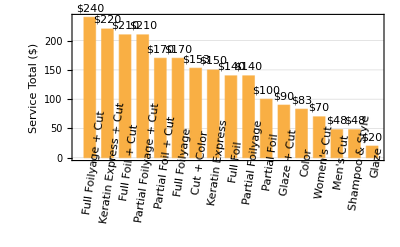

```mathematica
BarChart[data, PlotTheme-> "Business",Frame->True,FrameLabel->{None,"Service Total ($)"},LabelStyle->{FontFamily->"Times New Roman",GrayLevel[0]},ChartLabels->Placed[data2,Below,Rotate[#,Pi/2.2]&], LabelingFunction->(Placed[Row[{"$",#}],Above]&),BarSpacing->0.5]
```

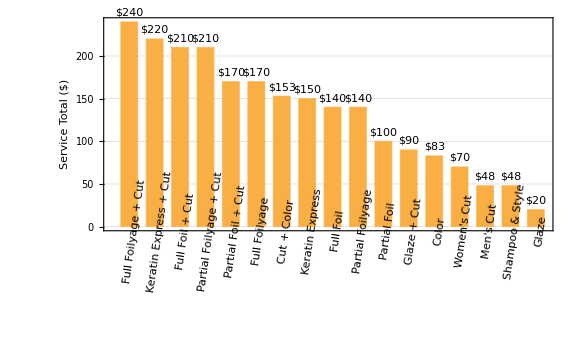

```mathematica
Show[%248,ImageSize->Large]
```

```mathematica
(240*n1)+220+210+210+170+170+153+150+140+140+100+90+83+70+48+48+20
```

```mathematica
2262
```

2262

```mathematica
%/17
```

2262/17

```mathematica
N[2262/17]
```

133.059

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17}

```mathematica
BarChart[data,PlotLabel->"GDP Per Capita",ChartLabels->Placed[countries,Below,Rotate[#,Pi/2.4]&]]
BarChart[{1,2,3},LabelingFunction->(Placed[Row[{"$",#}],Above]&)]
```

## Client List

```mathematica
Row[{"Adam Cox",Spacer[20],mensCut}]
Row[{"Alex Looney",Spacer[30],womensCut}]
Row[{"Alexis Goldman",Spacer[30],Combo2}]
Row[{"Alli Kuzma",Spacer[30],Combo1}]
Row[{"Allison Rogers",Spacer[30],Combo1}]
Row[{"Amy Mathews",Spacer[30],womensCut}]
Row[{"Amy Marsaudon",Spacer[30],womensCut}]
Row[{"Amy Minnick",Spacer[30],Combo1}]
Row[{"Andrew Mosteller",Spacer[30],mensCut}]
Row[{"Anna Rose Wascher",Spacer[30],Combo1}]
Row[{"Annette Cox",Spacer[30],womensCut}]
Row[{"April Woyshner",Spacer[30],womensCut}]
```

Adam Cox48

Alex Looney70

Alexis Goldman153

Alli Kuzma170

Allison Rogers170

Amy Mathews70

Amy Marsaudon70

Amy Minnick170

Andrew Mosteller48

Anna Rose Wascher170

Annette Cox70

SystemDialogInput::nprmtv: SystemDialogInput is not currently supported within preemptive evaluations.